```mathematica
Needs["QMB`"]
```

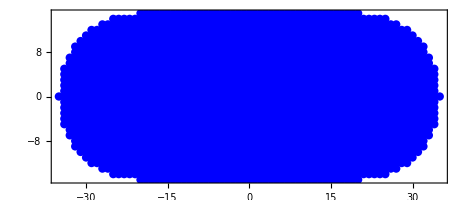

```mathematica
ListPlot[sitesStad,PlotStyle->{PointSize[0.015],Blue},AspectRatio->Automatic,Frame->True]
```

```mathematica
a=20;   (*longitud, a=rectangulo y R=esfera*)
R=15;
xMax=a+R;
yMax=R;
(*Ahora definiremos el estadio*)
inStadium[{x_,y_}]:=(Abs[x]<=a&&Abs[y]<=R)||(*rectangulo*)((x+a)^2+y^2<=R^2)||(*cirlulo*)((x-a)^2+y^2<=R^2);                (*igual, circulo*);
(*Ahora definimos un rectagulo*)
inRectangle[{x_,y_}]:=Abs[x]<=a&&Abs[y]<=R;
(*Crearemos la lista de todos los puntos en las geometrías*)
allSites=Flatten[Table[{x,y},{x,-xMax,xMax},{y,-yMax,yMax}],1];

sitesStad=Select[allSites,inStadium]; (*validos *)
sitesRect=Select[allSites,inRectangle];(*validos x2*)
(*Ahora los guardamos*)
dPosStad=Length[sitesStad];
dPosRect=Length[sitesRect];

siteIndexStad=AssociationThread[sitesStad->Range[dPosStad]];
siteIndexRect=AssociationThread[sitesRect->Range[dPosRect]];


dCoin=4;  (*por las 4 direcciones*)
dTotalStad=dCoin*dPosStad; 
dTotalRect=dCoin*dPosRect;
(*Agregado a partir de chatcito, tenía el error de que estaba usand matrices de dimensiones diferentes ???? se usa una mezcla de uniforme de todos los estados?????????*)
basisIndex[dPos_][c_,p_]:=1+c*dPos+(p-1);
J4=ConstantArray[1/4,{4,4}];   
CoinOp=2 J4-IdentityMatrix[4];
(*REVISAR QUE ONDA CON ESTO, POR QUÉ ME TIRA ERROR CON ?LA MONEDA??????*)
(*****Hasta acá chatgpt(para no perder)********)


MatrixForm[CoinOp]; (*matriz de la moneda*)

coinMoves={{+1,+1},{+1,-1},{-1,+1},{-1,-1}}; (*esto es lo mismo de la vez pasada, namas los movimientos, sirve para el operador de desplazamiento*)
buildShift[sites_List,siteIndex_Association,dPos_]:=(*operador de desplazamiento*)Module[{bIndex,rules},bIndex=basisIndex[dPos];
rules=Reap[Do[Module[{c,move,x,y,pos,sourceIndex,targetCoord,targetPosIndex},c=coin;
move=coinMoves[[c+1]];
pos=p;
{x,y}=sites[[pos]];
targetCoord={x,y}+move;
If[KeyExistsQ[siteIndex,targetCoord],targetPosIndex=siteIndex[targetCoord],targetPosIndex=siteIndex[{x,y}]];
sourceIndex=bIndex[c,pos];
Sow[{bIndex[c,targetPosIndex],sourceIndex}->1];],{coin,0,dCoin-1},{p,1,dPos}]][[2,1]];
SparseArray[rules,{dCoin*dPos,dCoin*dPos}]]; (*Esto sirve para definir las reglas de fontera, si llega al borde rebota, se construye el operador de desplazamiento y ya*)

Sstad=buildShift[sitesStad,siteIndexStad,dPosStad];
Srect=buildShift[sitesRect,siteIndexRect,dPosRect];

(*Ahora construimos los operadores de evolución como siempre se ha hecho*)
Ustad=(Sstad+Transpose[Sstad]).KroneckerProduct[CoinOp,IdentityMatrix[dPosStad]];
Urect=Srect.KroneckerProduct[CoinOp,IdentityMatrix[dPosRect]];
```

## P(r)

```mathematica
Sstad+Transpose[Sstad]
```

SparseArray[…]

Pureza en el dominio del estadio en t=0   = 1.

Pureza en el dominio del rectángulo en t=0 = 1.

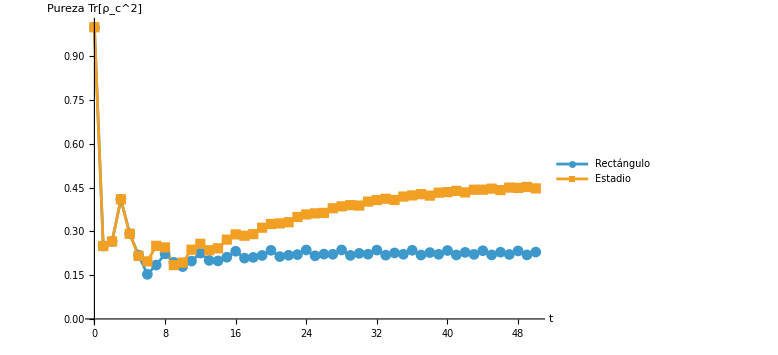

```mathematica
(*Ahora deiniremos el estado inicial y el origen*)
coin0={1,0,0,0};
centralCoord={0,0};
centralStad=If[KeyExistsQ[siteIndexStad,centralCoord],centralCoord,First@MinimalBy[sitesStad,Norm]];
centralRect=If[KeyExistsQ[siteIndexRect,centralCoord],centralCoord,First@MinimalBy[sitesRect,Norm]];

(*construiremos el estado inicial tanto para el estadio como para el rectángulo, esto ya solo lo tomamos de los otros .nb *)
pos0Stad=ConstantArray[0,dPosStad];
pos0Stad[[siteIndexStad[centralStad]]]=1;

pos0Rect=ConstantArray[0,dPosRect];
pos0Rect[[siteIndexRect[centralRect]]]=1;
psi0Stad=Normalize[Flatten[KroneckerProduct[coin0,pos0Stad]]];
psi0Rect=Normalize[Flatten[KroneckerProduct[coin0,pos0Rect]]];

(*evolución temporal*)
psiStad[0]:=psi0Stad;
psiStad[t_Integer?Positive]:=Nest[Ustad.#&,psi0Stad,t];
psiRect[0]:=psi0Rect;
psiRect[t_Integer?Positive]:=Nest[Urect.#&,psi0Rect,t];


(*Ahora síííí empezamos a contruir la matiz de densidad \et{\psi(t)}\bra{\psi(t)}*)
rhoTotalStad[t_Integer?NonNegative]:=(*entero y no negativo*)Module[{psiT},psiT=psiStad[t];
Outer[Times,psiT,Conjugate[psiT]]];
(*Lo mismo pero para el rectángulo*)
rhoTotalRect[t_Integer?NonNegative]:=Module[{psiT},psiT=psiRect[t];
Outer[Times,psiT,Conjugate[psiT]]];


(*AHora calcularemos la traza parcial*)
PartialTraceOverPosition[rho_,dPos_]:=Module[{rho4},rho4=ArrayReshape[rho,{dCoin,dPos,dCoin,dPos}];
TensorContract[rho4,{{2,4}}]];
rhoCoinStad[t_Integer?NonNegative]:=PartialTraceOverPosition[rhoTotalStad[t],dPosStad];
rhoCoinRect[t_Integer?NonNegative]:=PartialTraceOverPosition[rhoTotalRect[t],dPosRect];
MatrixForm[rhoCoinStad[0]];
MatrixForm[rhoCoinRect[0]];


(*Y la pureza :) que al final tuve que definir (el anterio también) aaaaaaaaaaah "Get: Cannot open ResourceFunction" a pesar de haberlo descargado y todo REVISAAAAAAAAAR*)

purityStad[t_Real?NonNegative]:=Module[{rhoC},rhoC=rhoCoinStad[t];
Tr[rhoC.rhoC]//N];

purityRect[t_Integer?NonNegative]:=Module[{rhoC},rhoC=rhoCoinRect[t];
Tr[rhoC.rhoC]//N];


tMax=50; (*valor máximo de pureza*)
(*calculo de las listas para la pureza*)
purityDataStad=Table[{t,purityStad[t]},{t,0,tMax}];
purityDataRect=Table[{t,purityRect[t]},{t,0,tMax}];
TableForm[purityDataRect[[1;;Min[10,Length[purityDataRect]]]]];
TableForm[purityDataStad[[1;;Min[10,Length[purityDataStad]]]]];
(*graficas*)
purezaPlot=ListLinePlot[{purityDataRect,purityDataStad},AxesLabel->{"t","Pureza Tr[ρ_c^2]"},PlotRange->{{0,tMax},{0,1.01}},PlotMarkers->Automatic,PlotLegends->{"Rectángulo","Estadio"},ImageSize->Large];

Print["Pureza en el dominio del estadio en t=0   = ",purityStad[0]];
Print["Pureza en el dominio del rectángulo en t=0 = ",purityRect[0]];

purezaPlot
```

```mathematica
Ustad
```

```mathematica
Tr[#.#]&@rhoCoinStad[10]
```

1659217803/8589934592